```mathematica
<<mf25.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m; so A(m) does not appear in the expansions. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
JnewCffList[6,3,x]
```

{1,744,196884,21493760,864299970,20245856256}

```mathematica
For[m=2,m<6,m++;
Print[J[5,m,X]]]
```

31/72+1/X+(1823 X)/27648+(10495 X^2)/2519424+(1778395 X^3)/18345885696

13/32+1/X+(1093 X)/16384+(47 X^2)/8192+(620001 X^3)/2147483648

79/200+1/X+(42877 X)/640000+(12957 X^2)/2000000+(1335816657 X^3)/3276800000000

7/18+1/X+(29 X)/432+(271 X^2)/39366+(269 X^3)/559872

```mathematica
For[m=2,m<6,m++;
Print[xJ[5,m,X]]]
```

1+(31 X)/72+(1823 X^2)/27648+(10495 X^3)/2519424+(1778395 X^4)/18345885696

1+(13 X)/32+(1093 X^2)/16384+(47 X^3)/8192+(620001 X^4)/2147483648

1+(79 X)/200+(42877 X^2)/640000+(12957 X^3)/2000000+(1335816657 X^4)/3276800000000

1+(7 X)/18+(29 X^2)/432+(271 X^3)/39366+(269 X^4)/559872

#### The functions below are Raleigh’s interpolating rational functions (p. 108). My code recovers them.

```mathematica
stream=OpenWrite["run20apr21no3"];
start=SessionTime[];
For[m=2,m<300,m++;
expansion=J[100,m,x];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 7240.140855

#### “run20apr21no3” is too large for github. I am going to create several shorter files.

```mathematica
rstream=OpenRead["run20apr21no3"];
list=ReadList[rstream];
Close[rstream];
Length[list]
```

298

```mathematica
rstream=OpenRead["run20apr21no3"];
list=ReadList[rstream];
Close[rstream];
wstream1=OpenWrite["run2jun21no11"];
For[j=0,j<50,j++;
Write[wstream1,list[[j]]]];
Close[wstream1];
wstream2=OpenWrite["run2jun21no12"];
For[j=0,j<50,j++;
Write[wstream2,list[[j+50]]]];
Close[wstream2];
wstream3=OpenWrite["run2jun21no13"];
For[j=0,j<50,j++;
Write[wstream3,list[[j+100]]]];
Close[wstream3];
wstream4=OpenWrite["run2jun21no14"];
For[j=0,j<48,j++;
Write[wstream4,list[[j+150]]]];
Close[wstream4]
```

run2jun21no14

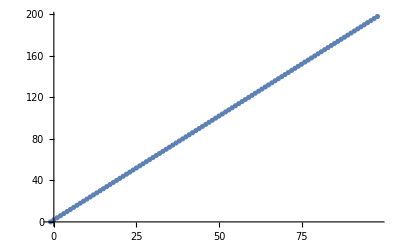

run20apr21no5

```mathematica
stream=OpenRead["run20apr21no3"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run20apr21no5"];
degrees={};
For[n=-2,n<98,n++;
data={};
For[k=0,k<298,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf*m^(2*n+2)}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
Length[list]
```

100

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
lastm=Last[list][[1]];
Print[{lastm,Length[list]}]
```

{98,100}

#### Check Raleigh’s first paper, p. 108, equation (III):

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
index=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
fm=factorIntoIrreducibleMonics[poly];
Print["================================================"];
Print["index: ",index];
Print[poly];
Print[fm]]
```

================================================

index: -1

1

{{1,1},{1,1}}

================================================

index: 0

1/2+(3 x^2)/8

{{3/8,1},{1,-1},{4/3+x^2,1}}

================================================

index: 1

-3/64-x^2/128+(69 x^4)/1024

{{69/1024,1},{1,-1},{-16/23-(8 x^2)/69+x^4,1}}

================================================

index: 2

1/54+x^2/216-(29 x^4)/864+x^6/128

{{1/128,1},{1,-1},{-2+x,1},{2+x,1},{-16/27-(8 x^2)/27+x^4,1}}

================================================

index: 3

-303/32768-(101 x^2)/32768+(5195 x^4)/262144-(3821 x^6)/524288+(5601 x^8)/8388608

{{5601/8388608,1},{1,-1},{-2+x,1},{2+x,1},{6464/1867+(11312 x^2)/5601-(38732 x^4)/5601+x^6,1}}

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
yes1=0;
no1=0;
yes2=0;
no2=0;
yes3=0;
no3=0;
yes4=0;
no4=0;
yes5=0;
no5=0;
yes6=0;
no6=0;


For[j=0,j<Length[list],j++;
n=list[[j,1]];
If[n>1,
poly=list[[j,2]];
fim=factorIntoIrreducibleMonics[poly];
last=First[Last[fim]];
If[monicPolynomialQ[last,x]==True,yes1++];
If[monicPolynomialQ[last,x]==False,no1++];
If[IrreduciblePolynomialQ[last]==True,yes2++];
If[IrreduciblePolynomialQ[last]==False,no2++];
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes3++];
If[Not[AllTrue[cl,rationalQ]],no3++];
degree=Exponent[last,x];
If[degree==2*n,yes4++];
If[degree≠2*n,no4++];
deglast=Exponent[last,x];
bad=0;
For[k=-1,k<deglast,k++;
cfk=Coefficient[last,x,k];
If[Mod[k,2]==0&&cfk==0,bad++];
If[Mod[k,2]==1&&cfk≠0,bad++]
];
If[bad==0,yes5++];
If[bad≠0,no5++];
If[Length[list2]==4&&list2[[2]]==-2+x&&list2[[3]]==2+x,yes6++];
If[Length[list2]!=4,no6++]
]

];
Print[{{yes1,no1},{yes2,no2},{yes3,no3},{yes4,no4},{yes5,no5},{yes6,no6}}]
```

{{97,0},{97,0},{97,0},{97,0},{97,0},{97,0}}

#### Make tables.

```mathematica
For[m=2,m<10,m++;
Print["m: ",m];
Print["  ",J[10,m,X]];
Print[]]
```

m: 3

31/72+1/X+(1823 X)/27648+(10495 X^2)/2519424+(1778395 X^3)/18345885696+(45767 X^4)/34828517376+(41650330075 X^5)/3327916660110655488+(711997 X^6)/7703510787293184+(1653962743405 X^7)/2944327674199660893831168+(1021044125 X^8)/349351379311776170508288

m: 4

13/32+1/X+(1093 X)/16384+(47 X^2)/8192+(620001 X^3)/2147483648+(653 X^4)/67108864+(9303515 X^5)/35184372088832+(52677 X^6)/8796093022208+(2206741887 X^7)/18446744073709551616+(77191 X^8)/36028797018963968

m: 5

79/200+1/X+(42877 X)/640000+(12957 X^2)/2000000+(1335816657 X^3)/3276800000000+(1493611203 X^4)/80000000000000+(1458495926643 X^5)/2097152000000000000+(64664568664389 X^6)/2867200000000000000000+(3494406888864013731 X^7)/5368709120000000000000000000+(23644062224068813 X^8)/1376256000000000000000000000

m: 6

7/18+1/X+(29 X)/432+(271 X^2)/39366+(269 X^3)/559872+(215 X^4)/8503056+(1741655 X^5)/1586874322944+(307 X^6)/7346640384+(491999 X^7)/342764853755904+(235733 X^8)/5205741216417792

m: 7

151/392+1/X+(165229 X)/2458624+(107365 X^2)/15059072+(25493858865 X^3)/48358655787008+(2771867459 X^4)/92561489592320+(168351462893475 X^5)/118895751725676756992+(36826135390421541 X^6)/624462781016702892113920+(20845419590657658847 X^7)/9354238358105289311446368256+(53674329840187738667 X^8)/690893631231484559139312500736

m: 8

49/128+1/X+(17629 X)/262144+(11465 X^2)/1572864+(307116945 X^3)/549755813888+(34283983 X^4)/1030792151040+(2150678672875 X^5)/1297036692682702848+(52614413973 X^6)/720575940379279360+(31836737635032599 X^7)/10880332376531662572355584+(83000417975587 X^8)/765023370224882524618752

m: 9

247/648+1/X+(150671 X)/2239488+(13589191 X^2)/1836660096+(69901012027 X^3)/120367356051456+(366770621371 X^4)/10282945612677120+(3257500444698134635 X^5)/1768591357765866863198208+(108551656609834559 X^6)/1289597865037611254415360+(2222620238316981329803361 X^7)/633718259619258503956804550000640+(641719347824464135620559 X^8)/4737105877202748260290391042949120

m: 10

19/50+1/X+(673 X)/10000+(701 X^2)/93750+(59679 X^3)/100000000+(2194921 X^4)/58593750000+(17843561 X^5)/9000000000000+(254289321 X^6)/2734375000000000+(89594891393 X^7)/22500000000000000000+(87629178911 X^8)/553710937500000000000

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<10,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
Print["   n: ",n];
Print["    ",poly];
Print[]]
```

n: -1

1

n: 0

1/2+(3 x^2)/8

n: 1

-3/64-x^2/128+(69 x^4)/1024

n: 2

1/54+x^2/216-(29 x^4)/864+x^6/128

n: 3

-303/32768-(101 x^2)/32768+(5195 x^4)/262144-(3821 x^6)/524288+(5601 x^8)/8388608

n: 4

373/72000+(373 x^2)/172800-(21809 x^4)/1728000+(7961 x^6)/1382400-(16367 x^8)/18432000+(3 x^10)/65536

n: 5

-4754693/1528823808-(4754693 x^2)/3057647616+(68420351 x^4)/8153726976-(106154827 x^6)/24461180928+(338577733 x^8)/391378894848-(2254159 x^10)/28991029248+(23003 x^12)/8589934592

n: 6

8241137/4214784000+(8241137 x^2)/7225344000-(4736509 x^4)/825753600+(288608923 x^6)/89915392000-(345473249 x^8)/462422016000+(23556341 x^10)/264241152000-(94778521 x^12)/17263755264000+(75 x^14)/536870912

n: 7

-165768344647/130459631616000-(165768344647 x^2)/195689447424000+(6257828375189 x^4)/1565515579392000-(491256042839 x^6)/208735410585600+(30381472425073 x^8)/50096498540544000-(4325861596609 x^10)/50096498540544000+(963243270647 x^12)/133590662774784000-(3307958239 x^14)/9895604649984000+(1881471 x^16)/281474976710656

n: 8

124848553201/147483721728000+(124848553201 x^2)/196644962304000-(185194889077 x^4)/65548320768000+(1351150410331 x^6)/786579849216000-(8955809117293 x^8)/18877916381184000+(1918266195107 x^10)/25170555174912000-(1168380534109 x^12)/151023331049472000+(298544975777 x^14)/604093324197888000-(19594805623 x^16)/1073943687462912000+(41 x^18)/137438953472

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<10,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
Print["   n: ",n];
Print["    ",Factor[poly]];
Print[]]
```

n: -1

1

n: 0

1/8 (4+3 x^2)

n: 1

(-48-8 x^2+69 x^4)/1024

n: 2

((-2+x) (2+x) (-16-8 x^2+27 x^4))/3456

n: 3

((-2+x) (2+x) (19392+11312 x^2-38732 x^4+5601 x^6))/8388608

n: 4

((-2+x) (2+x) (-286464-190976 x^2+650144 x^4-155904 x^6+10125 x^8))/221184000

n: 5

1/6262062317568(-2+x) (2+x) (4868805632+3651604224 x^2-12223806336 x^4+3737957344 x^6-419821596 x^8+16769187 x^10)

n: 6

1/207165063168000(-2+x) (2+x) (-101267091456-84389242880 x^2+275976533760 x^4-97244606208 x^6+14381852336 x^8-1021579752 x^10+28940625 x^12)

n: 7

1/25649407252758528000(-2+x) (2+x) (8147845676089344+7468858536415232 x^2-23764850390670336 x^4+9150173038346496 x^6-1601285210822720 x^8+153388981660272 x^10-7888431575988 x^12+171449044875 x^14)

n: 8

1/38661972748664832000(-2+x) (2+x) (-8182074782580736-8182074782580736 x^2+25262578868092928 x^4-10287291525124096 x^6+2013551386772992 x^8-233226372227840 x^10+16469761126016 x^12-659279330928 x^14+11533417875 x^16)